### Predicting outcomes based on rules a la Lanny Kirsch

```mathematica
{299459058088077823758143088095350287424,4,1}
```

```mathematica
getallmutations[{n_Integer, k_Integer, r_Integer}] :=
 Module[{digits = List/@IntegerDigits[n, k, k^(2r+1)], mudigs},
mudigs =(Tuples[ReplacePart[digits, #->Complement[Range[0, k - 1], digits[[#]]]]]&/@ Range[Length[digits]-1] )// Flatten[#, 1]&;
{#, k, r}&/@ (FromDigits[#, k]&/@ mudigs)
  ]
```

```mathematica
ng = NestGraph[getallmutations,{{299459058088077823758143088095350287424,4,1}},2];
```

```mathematica
vs = VertexList[ng];
```

```mathematica
alllts = ParallelMap[TestCALifeTime[CellularAutomaton[#, {{1}, 0}, 400]]&, vs];
```

```mathematica
Iconize[alllts]
```

```mathematica
nums = alllts/.-Infinity->405;
```

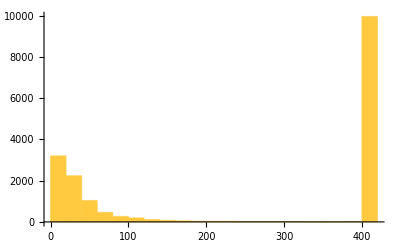

```mathematica
Histogram[nums]
```

```mathematica
alldigs = (IntegerDigits[#1, #2, #2^(2#3+1)]&)@@@vs;
```

```mathematica
SeedRandom[5555];
trainidxs = RandomSample[Range[Length[alllts]], 15000];
testidxs = Delete[Range[Length[alllts]], List/@ trainidxs];
```

#### Lifetime

```mathematica
Predict[alldigs[[trainidxs]]->nums[[trainidxs]]]
```

PredictorFunction[…]

```mathematica
pf = ;
```

```mathematica
preds = pf/@ alldigs[[testidxs]];
```

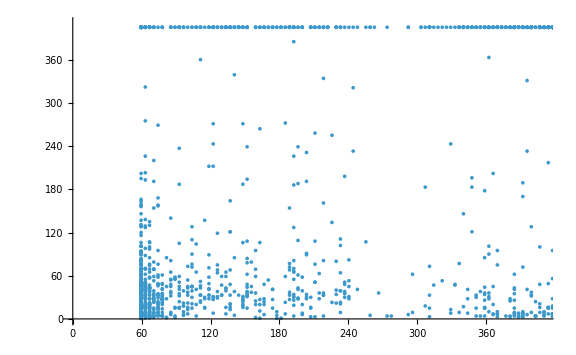

```mathematica
ListPlot[Transpose[{preds, nums[[testidxs]]}], PlotHighlighting->None, PlotRange->{{0, 410}, {0, 410}}]
```

#### Cancer or not

```mathematica
With[{ltbin =(If[# == -Infinity,"Cancer", "Non-Cancer"]&)/@alllts[[trainidxs]]},  Classify[alldigs[[trainidxs]]->ltbin]]
```

ClassifierFunction[…]

```mathematica
cf =;
```

```mathematica
cs  = cf/@ alldigs[[testidxs]];
```

```mathematica
ltbin =(If[# == -Infinity,"Cancer", "Non-Cancer"]&)/@alllts[[testidxs]];
```

```mathematica
With[{bools = MapThread[If[#1 == #2, True, False]&, {cs, ltbin}]},
N[Count[bools, True]/ Length[bools]]]
```

0.864113

```mathematica
N[Count[ltbin, "Cancer"] / Length[ltbin]]
```

0.549331

#### Looking for cancer “genes”

```mathematica
bools = MapThread[If[#1 == #2, True, False]&, {cs, ltbin}];
```

```mathematica
cancerrus = Pick[vs[[testidxs]], ltbin, "Cancer"];
```

```mathematica
noncancerrus =  Pick[vs[[testidxs]], ltbin, "Non-Cancer"];
```

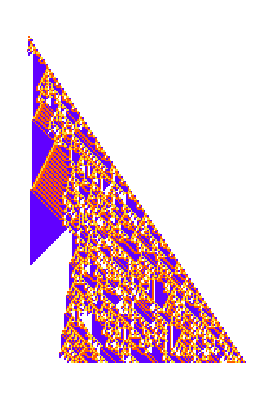
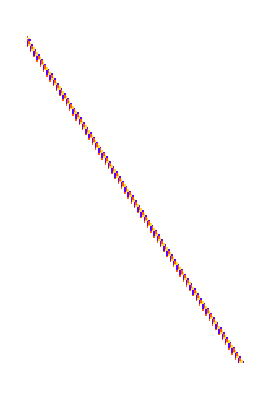
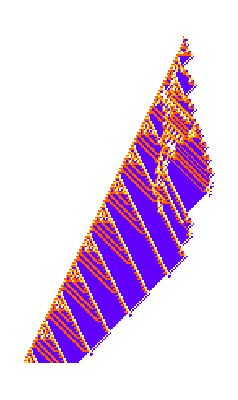
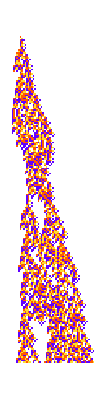
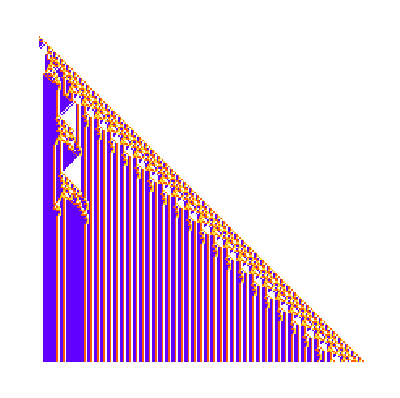
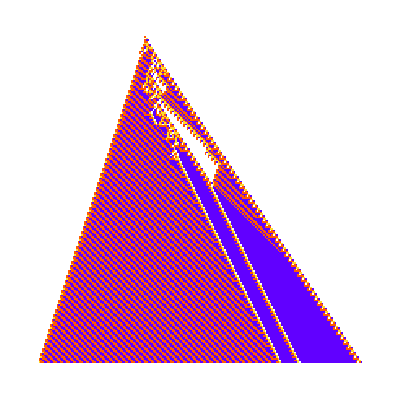
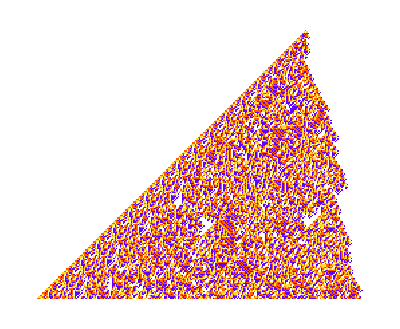
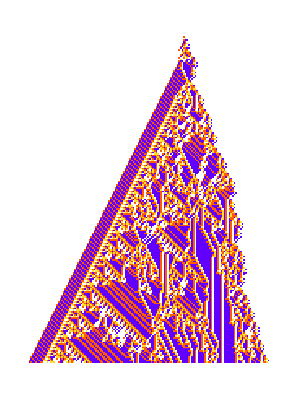
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[5555];
PlotCA/@RandomSample[cancerrus, 10]
```

```mathematica
cancerdigs = (IntegerDigits[#1, #2, #2^(2#3+1)]&)@@@cancerrus;
```

```mathematica
noncancerdigs = (IntegerDigits[#1, #2, #2^(2#3+1)]&)@@@noncancerrus;
```

```mathematica
initdigs = IntegerDigits[#1, #2, #2^(2#3+1)]&@@{299459058088077823758143088095350287424,4,1};
```

```mathematica
Transpose[cancerdigs]
```

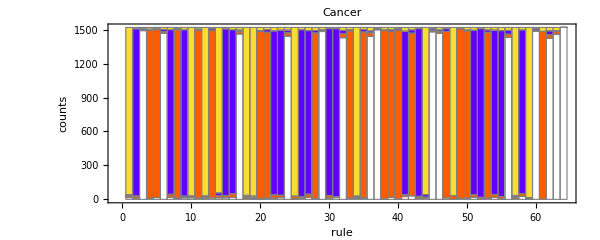
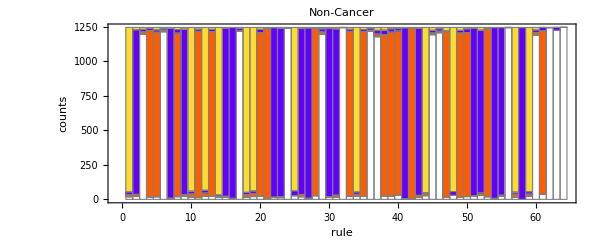

```mathematica
MapThread[Function[{digs,label}, With[{aps = Rasterize[ArrayPlot[List/@#,ImageSize->{10, 25}, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"](*, Mesh->True, MeshStyle->Opacity[.4]*)]]& /@ RuleTuples[4, 1]}, BarChart[MapIndexed[BinCounts[DeleteCases[#, initdigs[[#2]]], {0, 4, 1}]&,Transpose[digs]], ChartLayout->"Stacked", ChartBaseStyle->EdgeForm[Thickness[.1]], ChartStyle->(Directive[EdgeForm[Directive[Opacity[1], Gray]], #]&)/@ {{"[◼]", "CustomStyleData"}}["Colors"][[All, 2]], ChartLabels->{aps, None}, LabelingSize->35, AspectRatio->.4, ImageSize->{600, Automatic}, Frame->True, FrameLabel->{"rule", "counts"},PlotLabel->label]]],
{{cancerdigs,noncancerdigs}, {"Cancer", "Non-Cancer"}}]
```